# K-Complexity for Ising Model

## The Lanczos Algorithm (which needs improving)

The main trouble is with how long these algorithms take for large input matrices. 
From plotting the precision of the iterated variables as a function of n, we can see that there is a significant rate of precision loss mainly due to floating point arithmetic (according to my naive calculations). This precision loss can be as bad as 1 decimal per iteration. This means for large system size, which require a large number of iterations to converge, we need a crazy high precision. Large system size also means much bigger matrices. This causes a scaling where, for the system shown in the Testing station, L=5 takes a few seconds on my laptop, but L=7 takes more than a day on the HPC with 40 cores. And we’d ideally like to be able to calculate with L greater than 10   ...    :|

We define the inner product which we orthogonalize with respect to, and a commutator

```mathematica
MyInnerProd[A_,B_] := Module[{psi},psi = Tr[ConjugateTranspose[A].B]]
```

```mathematica
comm[Op1_,Op2_]:= Module[{com},com= Op1.Op2 - Op2.Op1]
```

For a simple explanation of the Lanczos algorithm see  https://arxiv.org/abs/2109.03824 . It will take a Hamiltonian and an Operator as an input, and give a set of Lanczos coefficients (b_n) as outputs.

“LanczosJacoAndChatGPT” is a slightly more optimized version of the algorithm in the above paper. 
In order to reduce precision loss at each iteration, we reorder the operations such that we do not need to use b[i] in order to calculate the values in the next iteration. This helps because in order to calculate b[i], we require a nasty square root. This change was suggested by Jaco.
I recently asked my new mate, ChatGPT, for suggestions to improve the efficiency of my code, and one of the things it suggested was pre-allocation of the arrays. Ordinarily this is an obviously beneficial thing to do - however I measured the difference in time, and it in fact takes marginally longer to run when pre-allocating the arrays than just defining initial values and then appending during the loop (This must be due to some crazy back-end Mathematica Magic^TM ).

```mathematica
LanczosJacoAndChatGPT[H_,S_,nmax_,precision_,btol_,bPrecision_] := Module[{b,Op,B,LOp ,NormSq, count,OpDim, tolval,i},
(*In order to improve efficiency we initialize and pre-allocate arrays of length nmax to prevent dynamic resizing of arrays in the loop*)
(*Op and LOp are arrays of matrices which are the dimension of S*)
count=0;
OpDim=Dimensions[S];
b=ConstantArray[0.,nmax];
NormSq=ConstantArray[0.,nmax];
B=ConstantArray[0.,nmax];
tolval=ConstantArray[0.,nmax];
Op=ConstantArray[0.,Join[{nmax},OpDim]];
LOp=ConstantArray[0.,Join[{nmax},OpDim]];

(*The first iteration is done outside loop to avoid divide by zero errors*)
Op[[1]] =  N[S,precision];                                                (*Making it numerical*)
NormSq[[1]]=MyInnerProd[Op[[1]],Op[[1]]];
LOp[[1]]=comm[H,Op[[1]]];
B[[1]]=MyInnerProd[Op[[0]],LOp[[1]]];
Op[[2]]=LOp[[1]];


Do[(*A couple of intermediary variables, to reduce repeat calculations. Worse space efficiency though*)
LOp[[i]]=comm[H,Op[[i]]];
NormSq[[i]]=MyInnerProd[Op[[i]],Op[[i]]];
B[[i]]=MyInnerProd[Op[[i-1]],LOp[[i]]];
tolval[[i]]=B[[i]]/NormSq[[i-1]];
(*The important step*)
Op[[i+1]] = LOp[[i]] - tolval[[i]]*Op[[i-1]];

If[N[tolval[[i]]]<btol,Print["Cut-off reached at n= ",i,", since tolval (b[i]/NormSq[i - 1]) and btol are ",tolval[[i]]," and ",btol]; 
(* Break when the (approximate) Lanczos coefficients reach close to zero. We want to catch this and break before we hit a div by zero error in the b[[i]]*)
Break[]];
b[[i]]=N[B[[i]]/Sqrt[NormSq[[i]]*NormSq[[i-1]]],bPrecision];
count++;
,{i,2,nmax}];
Table[b[[i]],{i,1,count}]]
```

In “LanczosDerick” , I did the obvious memory improvement of only storing the values needed to calculate the next iteration’s values. This was another improvement which turned out to be not as significant as I thought it should be  :(      (you can see by the difference in timing in the Testing Station section).

```mathematica
LanczosDerick[H_,S_,nmax_,precision_,btol_,bPrecision_] := Module[{b,Op1,Op2,Op3,B,LOp ,NormSq1,NormSq2,tolval, count,OpDim, i},
count=0;
b=ConstantArray[0.,nmax];


Op1=N[S,precision];
LOp=comm[H,Op1];
NormSq1=MyInnerProd[Op1,Op1];
Op2=LOp;

Do[(*A couple of intermediary values, to reduce repeat calculations*)
LOp=comm[H,Op2];
NormSq2=MyInnerProd[Op2,Op2];
B=MyInnerProd[Op1,LOp];
tolval=B/NormSq1;

(*The important step*)
Op3=LOp-tolval*Op1;

If[N[tolval]<btol,Print["Cut-off reached at n= ",i,", since tolval (b[i]/NormSq[i - 1]) and btol are ",tolval," and ",btol]; 
(* Break when the (approximate) Lanczos coefficients reach close to zero. We want to catch this and break before we hit a div by zero error in the b[[i]]*)
Break[]];
b[[i]]=N[B/Sqrt[NormSq1*NormSq2],precision];

(*Re-assign the dummy variables*)
Op1=Op2;
Op2=Op3;
NormSq1=NormSq2;
count++;
,{i,2,nmax}];
Table[b[[i]],{i,1,count}]]
```

## Generating Spin Matrices (don’t worry about it, it just gets used once to generate the input)

We need to convert our Spin operators into matrices. The matrices are made by taking Kronecker product along the chain of the operator at each site.

```mathematica
(*For Ising Matrix. Given a binary number occupation rep of spins, it gives the corresponding matrix*)
SpinStateMatrix[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*For Ising Matrix. Given Length, Interaction Spins, Number of Interaction Spins (k-local), And the Spins for 2 magnetic fields, it Generates the Matrix representation.*)
IsingSum[L_,IntSpin_,IntSpinNo_,BSpin1_,BSpin2_]:=Module[{IntPerms, IntPieces, IntPart, B1Part, B2Part, SingleSpinPerms, B1Pieces, B2Pieces},
IntPerms = Table[Join[ConstantArray[0,i-1],ConstantArray[1,IntSpinNo],ConstantArray[0,L-(i-1)-IntSpinNo]],{i,1,L-IntSpinNo+1}];
SingleSpinPerms=Table[Join[ConstantArray[0,i-1],ConstantArray[1,1],ConstantArray[0,L-(i-1)-1]],{i,1,L}];
If[IntSpin == 0, IntPart = IntSpin, IntPart =IntSpin,
IntPieces = Table[SpinStateMatrix[IntPerms[[i]], IntSpin],{i, 1, Length[IntPerms]}];
IntPart = Total[IntPieces]];
If[BSpin1 == 0, B1Part=BSpin1,B1Part=BSpin1,
B1Pieces=Table[SpinStateMatrix[SingleSpinPerms[[i]],BSpin1],{i,1,Length[SingleSpinPerms]}];
B1Part = Total[B1Pieces]];
If[BSpin2 == 0, B2Part = BSpin2,B2Part=BSpin2,
B2Pieces =Table[SpinStateMatrix[SingleSpinPerms[[j]],BSpin2],{j,1,Length[SingleSpinPerms]}];
B2Part = Total[B2Pieces]];
IntPart+B1Part+B2Part]
```

## Calculating K-Complexity from the Lanczos coefficients (I think I did a good job, its getting the Lanczos coefficients that’s the pain)

In order to extract the Krylov Complexity from the Lanczos coefficients we can solve the 1D particle hopping equation for phi
	∂_t ϕ  = ϕ_(n-1)b_n - b_(n-1)ϕ_(n+1)  
But the phi index starts from 0 and the b index starts from 1. So,  b_n->b_n+1 to match up the b’s with phi’s correctly. 
We also prepend and append 0 to the Lanczos coefficients. So thus b_1=0 and b_(m+2)=0.
    i.e.	  	∂_t ϕ_0  = b_1 ϕ_-1 - b_2 ϕ_1 ,    			 (but the first term vanishes since b_1=0) 
    	 	∂_t ϕ_1  = b_2 ϕ_0 - b_3 ϕ_2  ,
    	 	...
    	 	∂_t ϕ_n  = b_(n+1) ϕ_(n-1)- b_(n+2)ϕ_(n+1)  
    	 	...
    	 	∂_m ϕ_1  = b_(m+1)ϕ_(m-1) - b_(m+2)ϕ_(m+1)	(but the last term vanishes since b_(m+2)=0)
And now we can solve for ϕ_0 to ϕ_m.
And then use phi to find the Krylov-complexity and the normalized Krylov Complexity
	K(t)=∑_n n ϕ_n^*ϕ_n
K_norm(t)=(∑_n n ϕ_n^*ϕ_n)/(∑_n ϕ_n^*ϕ_n)

```mathematica
KComplexityFromBs[b_,bmax_,tmax_]:=Module[{ϕ,soln,bNew, bSlice,f,K,NormK},
(*Solve the particle hopping equation with Zero BC on n, and IC of Subscript[ϕ, n](0)= Subscript[δ, n](0)*)

bSlice=b[[;;bmax+1]];
bNew= Append[bSlice,0];
soln=NDSolve[Join[Table[D[ϕ[n,t],t]==
 bNew[[n+1]]*ϕ[n-1,t]- bNew[[n+2]]*ϕ[n+1,t],{n,0,bmax}],
Table[ϕ[n,0]==KroneckerDelta[n,0],{n,0,bmax}]],{Table[ϕ[n,t],{n,0,bmax}]},{t,0,tmax}];
(*Extract the phi's from the solution*)
f=soln[[1]][[1]][[2]];
(*Calculate the K-Complexity from the phi's*)
K = Sum[n*Conjugate[f[[n+1]]]*f[[n+1]],{n,1, bmax}]
]
```

```mathematica
NormKComplexityFromBs[b_,bmax_,tmax_]:=Module[{ϕ,soln,bNew, bSlice,f,K,NormK},
(*Solve the particle hopping equation with Zero BC on n, and IC of Subscript[ϕ, n](0)= Subscript[δ, n](0)*)

bSlice=b[[;;bmax+1]];
bNew= Append[bSlice,0];
soln=NDSolve[Join[Table[D[ϕ[n,t],t]==
 bNew[[n+1]]*ϕ[n-1,t]- bNew[[n+2]]*ϕ[n+1,t],{n,0,bmax}],
Table[ϕ[n,0]==KroneckerDelta[n,0],{n,0,bmax}]],{Table[ϕ[n,t],{n,0,bmax}]},{t,0,tmax}];
(*Extract the phi's from the solution*)
f=soln[[1]][[1]][[2]];
(*Calculate the Normalized K-Complexity from the phi's*)
NormK=Sum[n*Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]/Sum[Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]
]
```

## Testing Station

Now we can find the K-complexity for various operators and compare. 
Below we have the Hamiltonian for a Ising chain of length 4 with a transverse and longitudinal magnetic field.
	H = 	-J(σ_z  ⊗ σ_z ⊗ Id ⊗ Id) +  (Id ⊗ σ_z ⊗ σ_z ⊗ Id) + (Id ⊗ Id ⊗ σ_z ⊗ σ_z)
		+B1 (σ_z  ⊗ Id ⊗ Id ⊗ Id) +  (Id⊗ σ_z  ⊗ Id ⊗ Id)+ (Id ⊗ Id ⊗ σ_z  ⊗ Id) + (Id  ⊗ Id ⊗ Id ⊗ σ_z)
		+B2 (σ_x  ⊗ Id ⊗ Id ⊗ Id) +  (Id⊗ σ_x  ⊗ Id ⊗ Id)+ (Id ⊗ Id ⊗ σ_x  ⊗ Id) + (Id  ⊗ Id ⊗ Id ⊗ σ_x)
where we (for now) set J=B1=B2=1. This is the chaotic regime (where magnetic field strengths are comparable).
We will use the operators 
	Op1 =  (σ_z  ⊗ Id ⊗ Id ⊗ Id) +  (Id⊗ σ_z  ⊗ Id ⊗ Id)+ (Id ⊗ Id ⊗ σ_z  ⊗ Id) + (Id  ⊗ Id ⊗ Id ⊗ σ_z) 
	Op2 =  (σ_z  ⊗ σ_z ⊗ Id ⊗ Id) +  (Id ⊗ σ_z ⊗ σ_z ⊗ Id) + (Id ⊗ Id ⊗ σ_z ⊗ σ_z)
	Op3 =  (σ_z  ⊗ σ_z ⊗ σ_z ⊗ Id)+ (Id ⊗ σ_z  ⊗ σ_z ⊗ σ_z)

With this Hamiltonian and this type of reflective symmetric operator, the algorithm will converge in approximately 2^(2n-1)  iterations. So we set nmax to be larger than this value, if we want all the Lanczos coefficients. And given that the precision loss occasionally gets close to 1 digit per iteration, we use a precision of around nmax to ensure that we wont run out of float precision during the calculation.

Cut-off reached at n= 122, since tolval (b[i]/NormSq[i - 1]) and btol are 0. and 1/100000

{1.21063,Null}

Cut-off reached at n= 122, since tolval (b[i]/NormSq[i - 1]) and btol are 0. and 1/100000

{1.19196,Null}

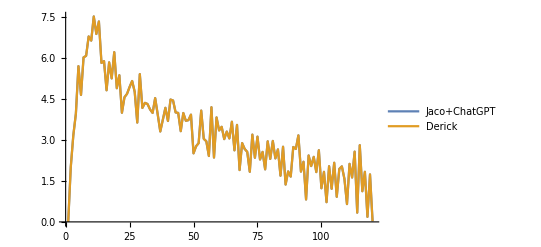

```mathematica
L=4;
prec=200;
nmax=200;
btol = 10^(-5);
H=IsingSum[L,PauliMatrix[3],2,PauliMatrix[3],PauliMatrix[1]];
Op=IsingSum[L,0,2,PauliMatrix[3],0];

(*Time the two algorithms, then plot the resultant Lanczos coefficients*)
AbsoluteTiming[bJacoAndChatGPT=LanczosJacoAndChatGPT[H,Op,nmax,prec,btol,10];]
AbsoluteTiming[bDerick=LanczosDerick[H,Op,nmax,prec,btol,10];]
ListLinePlot[{bJacoAndChatGPT,bDerick},PlotLegends->{"Jaco+ChatGPT","Derick"}]
```